# SurfCalc raft flatness 02.nb

2014.08.08 - Customized for raft flatness analysis of OGP data from SurfAnal 13 Freeform Cloud.nb.  Trimmed unnecessary expressions and plots.

2013.08.07 ver 13 - Rename the working arrays to clarify function.
2013.07.19 ver 12b - Added Chebyshev polynomial fit. Could not add display of fit coefficients vs order of the polynomial. Use MathGroup solutions to Hold and Release question.
2013.06.28 ver. 11 - Added section to read in separate REF cal file, clean it up, fit to a polynomial and then subtract the fit from the SUT data. This corrects for OGP systematic error.
2012.05.21 ver. 10a - Changed "sparse" variable name to "cloud". Modifed triplet text input to handle 4 or 5 or more numbers in a record. THen extract the XYZ values and continue.
2012.05.15 - Cleaned up OGP data input. Added BoxWhiskerPlot and better labeling. Only convert OGP z-values to microns.
2011.01.21 - Added IGES format for OGP files. Convert OGP triplets into integers (microns).
2010.09.27 - Modified for Quick Surface Scan data format.
2010.02.25 - Added Lanczos differentiator in 2D from Hamming book. Reduces high freq noise.
2009.12.15 ver. 9 - modified to handle variable row and column length for OGP data.
2009.06.22  ver.8 - Added general input file section for unknown formats. As shown for output from David's Keyence gantry program.
2008.05.07  ver. 7 -  Added function to plot discontinuous surfaces correctly showing blank regions. Requires setting bad ponts to imaginary value.
2008.03  Does GEM foil analysis
2008.02.18  Add H2S routines.
2007.05.19 ver.3 - Changed names of variables. Added tick function to scale index values into physical units.

2007.04.14
ver. 01 - Combines KeyDetectSurf 05  and SurfaceFlatness with bad points fixer.

Reads in Keyence area data from LabView file.

2007.04.01 Generalized the 2D surface fit function to any order in x&y.2006.12.20 Added Bad Data Point finder.

2007.02.18 -  Generalize surface fit to any order

PZT  2006 March 15 - KeyDetectSurf ver. 01

#### Reads in OGP ASCII data and Keyence area data from LabView file.

Data file is structured as a matrix of points. Entries are triplets of x,y,z values. Data is separated into scans. Data for each scan is arranged sequentially as row 1, row 2, etc. So the file is a list of scans, each scan is a list of rows, each row is a list of data triplets.

Note that the file is structured so that the x-value varies fastest. Triplets are arranged in rows in the file with the x-value changing fastest. One complete x-scan comprises a single row of data at a single y-value. The index for the x-value is the column identifier in the array,  the y-position is  the row identifier.

Need to strip off the z values and do statistics on them, keeping track of what x-y coord is of each z-value. THis is done by partitioning appropriately at the right time in the analysis.

Execute next statement first. It causes all of the initialization cells to be executed.

```mathematica
Button["Run Initialization first",FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

## 1. Initialize

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

```mathematica
Off[General::"spell1"]
(*<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
<<"LinearRegression`"*)
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

```mathematica
$OperatingSystem
```

```mathematica
snum$:=SessionTime[]//IntegerPart//ToString
```

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

## 2. Define statistical functions for profile data.

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

```mathematica
nPts
```

```mathematica
Length[psd2side]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

## 3. Enter path to desired file here. Default directory is set to the parent directory of this file.

Raft surface files

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/140808 SANDVIK Ce6 /SANDVIK raft box 01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01B/MF01B after polish box 1x1 01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/MF03 140812 after polish.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01A-01/after lightweighting/MF01A-01 140812 after polish 01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014/ECMpart01_full surf lines.DAT"
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

## Enter full file path here to set working directory:

```mathematica
filepathfull = "/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014/ECMpart01_full surf lines.DAT";
```

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"];
SelectionMove[nb,After,GeneratedCell]
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014

### Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
datain=.;datain2=.;datainXYZSR=.;
```

```mathematica
skipnum=1;
```

```mathematica
nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
(* {nRows,nCols,delx, dely}=Input["Enter nominal rows, cols and delx, dely values for the OGP scan point cloud.",{nRows,nCols,delx, dely}]*)
```

```mathematica
fnames=FileNames["*.DAT"];
```

```mathematica
Length[fnames]
```

5

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | ECMpart01_full surf box.DAT
2 | ECMpart01_full surf lines.DAT
3 | ECMpart01_full surf Y3mm_02.DAT
4 | ECMpart01_full surf Y3mm.DAT
5 | test01.DAT

#### Pick the OGP file from the list

First, reset the default working directory to the original filepath. Further down, the working directory gets reset to a subdir with the root name of the selected file.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014

```mathematica
inst$="OGP"
```

OGP

```mathematica
nf=Input["Enter index of file desired, 0 for Abort.",1]
```

4

```mathematica
If[nf==0,MessageDialog["Enter valid file number after Abort"];Abort]
```

```mathematica
fileinfull =fnames[[nf]]
```

ECMpart01_full surf Y3mm.DAT

```mathematica
fileinroot=FileBaseName[fileinfull]
```

ECMpart01_full surf Y3mm

```mathematica
fileinS=fileinroot;
```

If no REF file, set filein to fileinS name

```mathematica
filein=fileinS;
```

```mathematica
datain=Import[fileinfull,"Data"];
```

```mathematica
Dimensions[datain]
```

{4203}

```mathematica
datain[[1;;10]]
```

{{C:\DATA\Raft,baseplate,ECM,2014\Full,surf,Y3mm.RTN,11/26/2014,11:34:16,1},{Point,1},{1.04345,0.95871,-0.005828,mm},{},{Contour,2},{1.11533,0.886657,-0.002817,mm},{2.11532,0.881422,-0.001811,mm},{3.1153,0.875199,-0.00093,mm},{4.11528,0.868556,-0.000108,mm},{5.11526,0.862703,0.000478,mm}}

```mathematica
datain[[-10;;-1]]
```

{{120.163,123.194,0.122385,mm},{121.163,123.188,0.122723,mm},{122.163,123.183,0.122973,mm},{123.163,123.177,0.123324,mm},{124.163,123.171,0.129786,mm},{125.163,123.165,0.126211,mm},{126.163,123.159,0.104773,mm},{127.163,123.153,-0.020049,mm},{},{EOR}}

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014

```mathematica
workdir=fileinroot<>"_files"
```

ECMpart01_full surf Y3mm_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

ECMpart01_full surf Y3mm_files already exists. Using it for output.

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014/ECMpart01_full surf Y3mm_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
```

4203

```mathematica
datain2=Select[datain,Length[#]>0&];
```

```mathematica
Length[datain2]
```

4160

```mathematica
datain2=Select[datain2,NumericQ[#[[1]]]&];
```

```mathematica
Length[datain2]
```

4115

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Clean up unwanted points for single contour file.

```mathematica
contourPos=Position[datain,"Contour",2];
```

#### To extract only the first contour, Do next . MAKE INACTIVE CELLS

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[Length[contourPos]>1,
datain2=Take[datain2,{contourPos[[1,1]],contourPos[[2,1]]}];
datain2=Drop[datain2,1];(* Now drop the 2 ends *)
datain2=Drop[datain2,-2];
datain2=Select[datain2,(Length[#]!=0)&];
Print["Only first coutour is selected from this file. Continue at interrupt."];
Interrupt[]
]
```

```mathematica
datain2[[-10;;-1]]//MatrixForm
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

```mathematica
Dimensions[datain3x]
```

{4115,3}

Convert z-vals to microns:

```mathematica
datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];
```

```mathematica
xunit$="mm";yunit$="mm";zunit$="µm";
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
urdataS=datain3x;
```

```mathematica
(*Manipulate[urdataS[[i]],{i,1,Length[urdataS],1}]*)
```

### 1.) No REF correction needed

```mathematica
fitidxR$="NA" ; (* Default string for no REF corrections *)
```

```mathematica
nfRef=0;
```

```mathematica
fileinS
```

ECMpart01_full surf Y3mm

```mathematica
urdataSR=urdataS; (* No REF. Copy surface into SR array. *)
```

```mathematica
worksurf=urdataSR;(* Set the starting data to the ref corrected input data.*)
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Length[urdataSR]
```

4115

## Analyze FREEFORM, discontinuous surfaces here, not on uniform grid.

### Select region to work on. Reset cloudXYZ here.

```mathematica
(*sparseXYZ=Take[bigDatalist,All,{2,4}];*)
```

```mathematica
skipnum=.;
```

```mathematica
MessageDialog["Need to ABORT and start from above to reset to original urdata. "]
```

ayvkk_shm70FrontEndObject[LinkObject["ayvkk_shm", 3, 1]]7070

```mathematica
{xunit$,yunit$,zunit$}
```

{mm,mm,µm}

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from worksurf based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the worksurf as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[worksurf,All,{1}]//Flatten;
yvals=Take[worksurf,All,{2}]//Flatten;
zvals=Take[worksurf,All,{3}]//Flatten;
```

```mathematica
{Mean[xvals],Mean[yvals],Mean[zvals]}//N
```

{63.8555,61.1965,1.14656×10^-15}

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{1.16533,63.8555,127.706}

{0.159905,61.1965,123.878}

{-6.17976,1.14656×10^-15,5.21657}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{126.541,123.718,11.3963}

```mathematica
rowscols$="sparse"
```

sparse

```mathematica
(*{nrows,ncols}={nRows,nCols}*)
```

Next expression does not contain desired array on first pass. Why????

```mathematica
Length[worksurf]
```

3037

```mathematica
lpp01=ListPointPlot3D[worksurf,PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS]
```

-Graphics3D-

```mathematica
stepinc=deltax;
```

```mathematica
stepinc=1.;
```

```mathematica
imin=xmin;imax=xmax;jmin=ymin;jmax=ymax;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Manipulate[Show[lpp01,PlotRange->{{imin,imax},{jmin,jmax},All}]
,{{imin,xmin},xmin,imax,stepinc},{{imax,xmax},imin,xmax,stepinc}
,{{jmin,ymin},ymin,jmax,stepinc},{{jmax,ymax},jmin,ymax,stepinc},LocalizeVariables->False]
```

```mathematica
corner$="";
```

```mathematica
xyrange={{imin,imax},{jmin,jmax}}
```

{{1.16533,127.706},{0.159905,123.878}}

```mathematica
corner$=ToString[imin//IntegerPart]<>"-"<>ToString[jmin//IntegerPart]
```

1-0

```mathematica
(* MemoryInUse[] *)
```

```mathematica
(* Manipulate[worksurf[[i]],{i,1,Length[worksurf],1},SaveDefinitions->True] *)
```

```mathematica
diffs=Differences[zvals];
```

Histogram all of the zvals, no skip.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

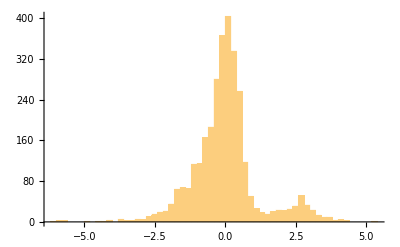

```mathematica
hist01=Histogram[zvals//Flatten,50,ImageSize->400];
{hist01,Dynamic[MousePosition["Graphics"]]}
```

### Execute each point removal section separately and reset worksurf each time. Start next iteration above.

#### XY Range clean up next. Do each section separately, resetting the main lists each time to the smaller ones.

trim after setting x and y ranges above

Reset the xy limits based upon above sliders.

```mathematica
xyrange={{imin,imax},{jmin,jmax}};
{{xmin,xmax},{ymin,ymax}}=xyrange;
{{xmin,xmax},{ymin,ymax},{zmin,zmax}};
{xrange,yrange,zrange}={{xmin,xmax},{ymin,ymax},{zmin,zmax}}
```

{{1.16533,127.706},{0.159905,123.878},{-6.17976,5.21657}}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
zrange =Input["Enter zrange values to trim data according to above histogram",zrange]
```

{-2.8,1.54}

```mathematica
{zmin,zmax}=zrange;
```

```mathematica
xvals=Take[worksurf,All,{1}]//Flatten;
yvals=Take[worksurf,All,{2}]//Flatten;
zvals=Take[worksurf,All,{3}]//Flatten;
deltax=xmax-xmin;deltay=ymax-ymin;deltaz=zmax-zmin;{deltax,deltay,deltaz}
```

{126.541,123.718,4.34}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Skip to other clean-up section based on statistics, if desired. Restrict here by x and y range numbers.
NEVER reset worksurf. This is the unaltered input data.

```mathematica
Length[worksurf]
```

3037

```mathematica
test =Reap[ Do[If[worksurf[[i]][[3]]<zrange[[2]]&& worksurf[[i]][[3]]>zrange[[1]]&&worksurf[[i]][[2]]<yrange[[2]]&& worksurf[[i]][[2]]>yrange[[1]]&&worksurf[[i]][[1]]<xrange[[2]]&& worksurf[[i]][[1]]>xrange[[1]],Sow[worksurf[[i]]]],{i,Length[worksurf]}]];
```

```mathematica
Short[test]
```

{Null,{{{2.11532,0.881422,-0.500141},{«1»},«2727»,{«1»},«1»}}}

```mathematica
trimsurf=Drop[test,1]//Flatten[#,2]&;
Length[trimsurf]
Remove[test];
```

2731

```mathematica
xvals=Take[trimsurf,All,{1}]//Flatten;
yvals=Take[trimsurf,All,{2}]//Flatten;
zvals=Take[trimsurf,All,{3}]//Flatten;
```

Subtract mean from z. Skip if integer.

```mathematica
meanz=Mean[zvals]//N
```

-0.219883

```mathematica
trimsurf=Map[MapAt[Plus[#,-meanz]&,#,3]&,trimsurf];
```

```mathematica
xvals=Take[trimsurf,All,{1}]//Flatten;
yvals=Take[trimsurf,All,{2}]//Flatten;
zvals=Take[trimsurf,All,{3}]//Flatten;
```

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N;
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N;
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{-2.55714,-2.38844×10^-16,1.74532}

```mathematica
{deltax=xmax-xmin, deltay=ymax-ymin,deltaz=zmax-zmin}
```

{126.441,123.705,4.30246}

```mathematica
Length[trimsurf]
```

2731

#### Plot after trimming the X or Y range above. TRIM IT IN PLACE.

```mathematica
lpp02=ListPointPlot3D[trimsurf,PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Show[lpp02,ViewPoint->{-2.918,-1.612,0.58}]
```

-Graphics3D-

## End of range clean-up iteration section. Contine after subregion is selected.

```mathematica
npts=Length[zvals]
```

2731

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

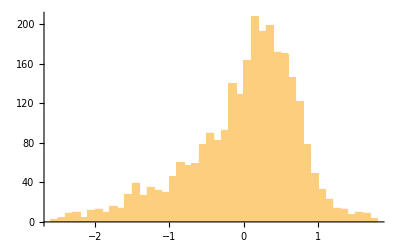

```mathematica
histplt=Histogram[zvals,50,ImageSize->400];
{histplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
zsd=StandardDeviation[zvals]//N
```

0.728552

### Enter the Z trim min and max based on the above histogram. This histogram gets narrower after the plane fit is subtracted. Subsequent passes identify most of the outlier points.

```mathematica
zminlist={};zmaxlist={};
```

```mathematica
{minq,maxq}={zmin,zmax}(*These are the extrema in the above histogram *)
```

{-2.55714,1.74532}

```mathematica
{minq,maxq} =Input["Enter zrange values to trim data according to above histogram",{minq,maxq}]
```

{-2.55714,1.74532}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
MessageDialog["Execute next section after specifying bad points above"];
```

#### Select the appropriate Z trim criteria next. Leave lists empty to use all points without discarding any. (Inactive cells)

```mathematica
zminlist={};zmaxlist={};
```

```mathematica
3zsd
```

2.01832

```mathematica
med=Median[zvals]
```

0.0780404

```mathematica
meanz=Mean[zvals]
```

-1.33727×10^-16

```mathematica
iqr=InterquartileRange[zvals]
```

0.836398

```mathematica
{minq,maxq}={med-2 iqr,med+2 iqr}
```

{-1.59476,1.75084}

```mathematica
{minq,maxq}={med-3 iqr,med+3 iqr}
```

{-2.43115,2.58724}

```mathematica
{minq,maxq}={meanz-4 zsd,meanz+4 zsd}
```

{-2.69109,2.69109}

```mathematica
{minq,maxq}={meanz-3 zsd,meanz+3 zsd}
```

{-2.01832,2.01832}

```mathematica
{minq,maxq}={meanz-2 zsd,meanz+2 zsd}
```

{-1.34554,1.34554}

```mathematica
{minq,maxq}={-2.5,3.6}
```

{-2.5,3.6}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Input["Select desired range from above, then execute next expression"]
```

### Continue here after selecting points to discard, or if no points to discard. Skip if nothing to trim.

```mathematica
zmaxlist=Select[zvals,#> maxq &];
zminlist=Select[zvals,#< minq &];
```

```mathematica
{Length[zmaxlist],Length[zminlist]}
```

{0,0}

```mathematica
Union[zmaxlist];
```

```mathematica
Length[%]
```

0

```mathematica
outliers=Join[zminlist,zmaxlist];
```

```mathematica
outliers2=Union[outliers];
```

```mathematica
plist=Table[Position[zvals,outliers2[[i]]],{i,Length[outliers2]}];
```

```mathematica
plist=Flatten[plist,1];
```

```mathematica
trimsurf=Delete[trimsurf,plist];
```

Discard points from the list that lie outside the desired range. Note that the result is a list, not an array. Can't use plot functions that require an array for input.

top is a reduced-size array to use in fitting the surface to avoid excessive calculation time. reduce=1 uses all the points.

```mathematica
top=.
```

Shorten the data array only if there are too many points. Need to change skipnum value first

```mathematica
zsdev=StandardDeviation[trimsurf][[3]]//N
```

0.728552

```mathematica
rowscols$="sparse";ToString[{nRows,nCols}]
```

{nRows, nCols}

```mathematica
topplt=ListPointPlot3D[trimsurf,PlotLabel->fileinS<>"\n{rows,cols}="<>rowscols$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

Set the worksurf to the above trimsurf. Go back up to trim more if desired.

```mathematica
worksurf=trimsurf;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Loop up to trim more points, if desired",NotebookLocate["Start trim"]]
```

Loop up to trim more points, if desired

## Fit polynomial surface to the point cloud

### Fit edited list to a surface. Enter the surface fit order next. A general set of basis polynomials is calculated and the fit is performed. Enter the x and y orders separately

Select one of the button options, then continue

```mathematica
fitflag=.;fitidxS$=.;fitord$=.
```

```mathematica
fitnumflag=Input["Enter num for fit to apply.\n0 = piston only\n1 = pure plane\n2 = pure sphere\n3 = general {m,n}order polynomial\n4 = Chebyshev polynomial (m,n)" ]
```

3

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### COntinue after fit selection

The working array is worksurf. Make sure it has the desired data in it.

Need to normalize the x and y values when doing the Chebyshev fit, using the actual values for xlen and ylen. For the other cases, use xlen=ylen=1 in the normaization expression.

```mathematica
xlen=1;ylen=1;
```

```mathematica
Switch[fitnumflag,
0,(*Piston only*)fitbasis={1};fitidxS$="0";fitidxS$="0";Print["Piston only fit"],
1, (*Pure Plane*)fitbasis={1,x,y};fitidxS$="S1,1"(*fitord$=StringTake[ToString[fitbasis],{2,-2}]*),
2,(*Pure Sphere*)fitbasis={1,x,y,x y,x^2+y^2};fitidxS$="Ssph"(*fitord$=StringTake[ToString[fitbasis//InputForm],{2,-2}]*),
3,(*General cartesian polynomial*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitidxS$="S"<>fitidxS$;
(*fitord$=StringTake[ToString[sp],{2,-2}];*)
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j]],{i,0,ordx},{j,ordy,0,-1}],
4,(*Chebychev poly*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitidxS$="S"<>"Chb"<>fitidxS$;
(*fitord$=StringTake[ToString[sp],{2,-2}];*)
(*compute the required xlen and ylen for this case*)
xlen=xmax-xmin//N;ylen=ymax-ymin//N;
fitbasis={};
xs[x_,xmax_,xmin_]:=2/(xmax-xmin) (x-xmin-(xmax-xmin)/2);
fitbasis=Table[HoldForm[ChebyshevT[ii,xs[x,xmax,xmin]]] HoldForm[ChebyshevT[jj,xs[y,ymax,ymin]]]/.ii->i/.jj->j,{i,0,ordx},{j,0,ordy}]//Flatten;

]
```

```mathematica
fitbasis//ReleaseHold//ColumnForm;
```

```mathematica
fitidxS$
```

S2,2

For Chebyshev, need to release the hold, then Sort the fitbasis to get it in the same order as comes out of the Fit result.
Need to sort the expanded funtions in terms of the highest powers of x and y. Sorting on y lets x-index run fast. This seems to work on both lists.

```mathematica
(*fitbasis2=fitbasis//ReleaseHold;
fitbasissort=fitbasis2//Sort[#,((Exponent[#1,y]<=Exponent[#2,y])&&True)&]&;
fitbasissort//ColumnForm  *)
```

Now calc and sort the fit expression. Need to convert the Head Plus to List by Apply.

```mathematica
surffit=Fit[worksurf,fitbasis//ReleaseHold,{x,y}];
```

```mathematica
surffit//OutputForm
```

2
0.163099 + 0.00358131 x - 0.0000967995 x  - 0.0162301 y + 0.000802945 x y - 
 
            -6  2                   2             -6    2             -8  2  2
  5.16512 10   x  y + 0.0000196588 y  - 3.75429 10   x y  + 2.98112 10   x  y

```mathematica
xrange
```

{1.16533,127.706}

```mathematica
Apply[List,surffit]//ColumnForm
```

0.163099
0.00358131 x
-0.0000967995 x^2
-0.0162301 y
0.000802945 x y
-5.16512×10^-6 x^2 y
0.0000196588 y^2
-3.75429×10^-6 x y^2
2.98112×10^-8 x^2 y^2

Find Max and Min points in the fit surface within the region of the raft. Use NMinimize and NMaximize to find global min and max. The FindMin and FindMax only find local extrema and are subject to roundoff errors.

```mathematica
region=Rectangle[{xmin,ymin},{xmax,ymax}]
```

Rectangle[{1.21533,0.165774},{127.656,123.871}]

```mathematica
maxsurffit=NMaximize[{surffit,{x,y}∈region},{x,y}]
```

{0.195728,{x→19.0179,y→0.165774}}

```mathematica
minsurffit=NMinimize[{surffit,{x,y}∈region},{x,y}]
```

{-0.956828,{x→127.656,y→0.165774}}

```mathematica
PVsurffit=maxsurffit[[1]]-minsurffit[[1]]
```

1.15256

Output the fit equations here, with the max and min stats.

```mathematica
snumfixed$=snum$
```

1780

```mathematica
filestats$="Surffit_"<>ToString[Length[worksurf]]<>"_"<>fitidxS$<>"_"<>snumfixed$ (*Text format*)
```

Surffit_2731_S2,2_1780

```mathematica
surffitstats =fileinS<>"\nFit order = "<>fitidxS$<>"\nSurface region corners = "<>ToString[region]
```

ECMpart01_full surf Y3mm
Fit order = S2,2
Surface region corners = Rectangle[{1.21533, 0.165774}, {127.656, 123.871}]

```mathematica
Head[surffitstats]
```

String

```mathematica
surffitstats=StringJoin[surffitstats,"\nMax value of surface = "<>ToString[maxsurffit]];
surffitstats=StringJoin[surffitstats,"\nMin value of surface = "<>ToString[minsurffit]];
surffitstats=StringJoin[surffitstats,"\nPV height difference = "<>ToString[PVsurffit]];
surffitstats=StringJoin[surffitstats,"\nFit eqn:\n"<>ToString[Apply[List,surffit,Heads->True]//OutputForm]]
```

ECMpart01_full surf Y3mm
Fit order = S2,2
Surface region corners = Rectangle[{1.21533, 0.165774}, {127.656, 123.871}]
Max value of surface = {0.195728, {x -> 19.0179, y -> 0.165774}}
Min value of surface = {-0.956828, {x -> 127.656, y -> 0.165774}}
PV height difference = 1.15256
Fit eqn:
                                        2                                            -6  2                  2             -6    2            -8  2  2
{0.163099, 0.00358131 x, -0.0000967995 x , -0.0162301 y, 0.000802945 x y, -5.16512 10   x  y, 0.0000196588 y , -3.75429 10   x y , 2.98112 10   x  y }

```mathematica
Button["Output the min and max stats for the current surface fit",Export[filestats$,surffitstats,"Text"]]
```

Output the min and max stats for the current surface fit

Add separate case here for Chebyshev. Normalize the x and y values before fittiing.

```mathematica
temp=worksurf;
```

```mathematica
temp=Map[MapAt[Divide[#,xlen]&,#,1]&,temp];
temp=Map[MapAt[Divide[#,ylen]&,#,2]&,temp];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
fitsurfplt=Plot3D[surffit,{x,xmin,xmax},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nSfit:"<>fitidxS$]
```

-Graphics3D-

```mathematica
Button["Export fit surface plot file",Export[foutname2<>"_fitsurf_"<>snum$<>".tiff",fitsurfplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export fit surface plot file

```mathematica
surfwfitplt=Show[topplt,fitsurfplt,PlotLabel->fileinS<>"\nSfit:"<>fitidxS$<>" with fit surf before subt"]
```

-Graphics3D-

```mathematica
Button["Export surface and fit plot file",Export[foutname2<>"_surfwfit_"<>snum$<>".tiff",surfwfitplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export surface and fit plot file

Subtract the selected fit from the data. Default is plane fit subtraction.

```mathematica
meanXYZdetrend=.;meanXYZtd=.;resids=.;
```

```mathematica
detrworksurf=Table[{worksurf[[i,1]],worksurf[[i,2]],worksurf[[i,3]]-surffit/.x->worksurf[[i,1]]/.y->worksurf[[i,2]]}
,{i,1,Length[worksurf]}
];
```

```mathematica
zresids=.
```

```mathematica
zcloudresids=Take[detrworksurf,All,{3}]//Flatten;
```

```mathematica
maxz=Max[zcloudresids];minz=Min[zcloudresids];sigma=StandardDeviation[zcloudresids];
```

```mathematica
sig$=ToString[sigma//NumberForm[#,{6,2}]&]
```

0.59

```mathematica
{maxz,minz,sigma}
```

{2.52669,-2.65972,0.586134}

```mathematica
Short[zcloudresids]
```

{-0.0997065,0.357197,«2728»,-0.148815}

```mathematica
zbin=BinCounts[zcloudresids,(maxz-minz)/50];
```

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

```mathematica
hgtrange=.
```

```mathematica
PV95rangelist=hrange[zcloudresids,0.025,0.975];
PV95range$=ToString[PV95rangelist//NumberForm[#,{6,2}]&];
PV95val=PV95rangelist[[2]]-PV95rangelist[[1]]
PV95$=ToString[PV95val//NumberForm[#,{6,2}]&]
```

2.44879

2.45

```mathematica
PV99rangelist=hrange[zcloudresids,0.005,0.995];
PV99range$=ToString[PV99rangelist//NumberForm[#,{6,2}]&];
PV99val=PV99rangelist[[2]]-PV99rangelist[[1]]
PV99$=ToString[PV99val//NumberForm[#,{6,2}]&]
```

4.14774

4.15

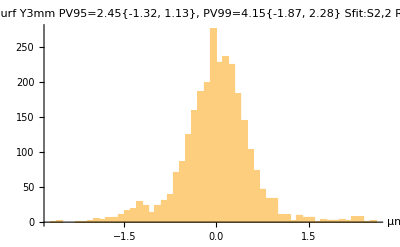

```mathematica
histresidplt=Histogram[zcloudresids,50,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10],AxesLabel->{zunit$,""},PlotLabel->fileinS<>"\nPV95="<>PV95$<>PV95range$<>", PV99="<>PV99$<>PV99range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$]
```

```mathematica
Button["Export histresid plot file",Export[foutname2<>"_histSR_"<>snum$<>".tiff",histresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histresid plot file

```mathematica
accumulatedCount[bins_,counts_]:=Accumulate[counts]
```

```mathematica
hrange[zcloudresids,0.025,0.975]
```

{-1.32049,1.1283}

```mathematica
hrange[zcloudresids,0.005,0.995]
```

{-1.86928,2.27845}

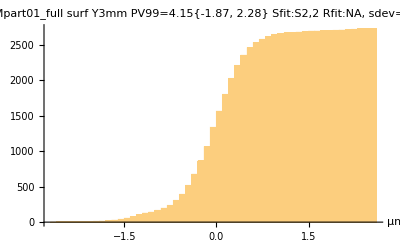

```mathematica
histcumplt=Histogram[zcloudresids,50,accumulatedCount,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10],PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
Button["Export histcum plot file",Export[foutname2<>"_histcumSR_"<>snum$<>".tiff",histcumplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histcum plot file

```mathematica
quantlist={0.0,0.005,0.01,0.025,0.50,.975,0.99,0.995,1.0};
```

```mathematica
qres=Quantile[zcloudresids,quantlist]
```

{-2.65972,-1.86928,-1.63705,-1.32049,0.0103262,1.1283,1.95007,2.27845,2.52669}

```mathematica
qtable=Transpose[{quantlist,qres}]//TableForm
```

0. | -2.65972
0.005 | -1.86928
0.01 | -1.63705
0.025 | -1.32049
0.5 | 0.0103262
0.975 | 1.1283
0.99 | 1.95007
0.995 | 2.27845
1. | 2.52669

```mathematica
q99range=qres[[8]]-qres[[2]]
```

4.14774

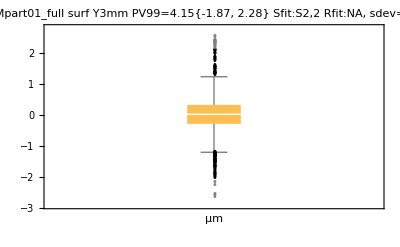

```mathematica
bwc=BoxWhiskerChart[zcloudresids,"Outliers",BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10],PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
Button["Export box whisker chart file",Export[foutname2<>"_boxwhisker_"<>snum$<>".tiff",bwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export box whisker chart file

```mathematica
fitidxS$
```

S2,2

Write out the quantile info to xls file and all zresids to text file.

```mathematica
Export[fileinS<>"-"<>sig$<>"_"<>fitidxS$<>"_"<>snum$<>"_zresids.txt",zcloudresids,"Text"]
```

ECMpart01_full surf Y3mm-0.59_S2,2_1782_zresids.txt

```mathematica
Export[fileinS<>"-"<>sig$<>"_"<>fitidxS$<>"_"<>snum$<>"_Quantiles.xls",qtable,"XLS"]
```

ECMpart01_full surf Y3mm-0.59_S2,2_1782_Quantiles.xls

```mathematica
binwid=(maxz-minz)/25;
```

```mathematica
bcts=BinCounts[zcloudresids,binwid];
```

```mathematica
sd=sigma//N
```

0.586134

```mathematica
MeanDeviation[zcloudresids]//N
```

0.417557

```mathematica
MedianDeviation[zcloudresids]
```

0.305565

```mathematica
zwid=4 sd
```

2.34454

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Plot detrended trim array. Eliminate the dropouts with the RegionFunction.

```mathematica
{minz,maxz}={Min[zcloudresids],Max[zcloudresids]}
```

{-2.65972,2.52669}

```mathematica
PV=maxz-minz
zrange={minz,maxz}
```

5.18641

{-2.65972,2.52669}

```mathematica
vp={0.85,-1.56,1.25};
```

This is corect way to make viewpoint dynamic:

```mathematica
Dynamic[vp]
```

Plot detrended point cloud next:

```mathematica
lpplt=ListPointPlot3D[detrworksurf,PlotRange->All,ColorFunction->"Rainbow",ViewPoint->Dynamic[vp],(*BoxRatios->{Automatic,Automatic,Automatic},*)AxesLabel->{"Xval","Yval","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]]
```

-Graphics3D-

```mathematica
legendplt=ContourPlot[y,{x,0,(maxz-minz)},{y,minz,maxz},ColorFunction->"Rainbow",AspectRatio->10,(*PlotRange->{{0,zwid/4},{-zwid/1,zwid/1}},*)PlotRangePadding->0,FrameTicks->{{Automatic,None},{None,None}},ImageSize->40];
```

```mathematica
foutname2=fileinS<>"_"<>"S"<>fitidxS$<>"_"
```

ECMpart01_full surf Y3mm_SS2,2_

```mathematica
lpplt2=With[{xx=0,yy=0,zz=Infinity},Row[{Show[lpplt,ViewPoint->Dynamic[vp]],legendplt},Spacer[10]]]
```

-Graphics3D--Graphics-

```mathematica
snum$
```

1783

```mathematica
Button["Export lpplt2 plot file",fnameplt=foutname2<>"_"<>snum$<>"_pts.tiff";Export[fnameplt,lpplt2,"ImageEncoding"->"LZW",ImageResolution->100];Print[fnameplt],Method->"Queued"]
```

Export lpplt2 plot file

ECMpart01_full surf Y3mm_SS2,2__1800_pts.tiff

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014/ECMpart01_full surf Y3mm_files

Output the detrended data triplets

```mathematica
Button["Export detrworksurf data text file",Export[foutname2<>"_"<>snum$<>"_DetrendXYZ.txt",detrworksurf,"Text"],Method->"Queued"]
```

Export detrworksurf data text file

Define a tick function to scale the values by some scaleval factor

```mathematica
ticksw[wmin_,wmax_,scaleval_,interval_]:=Table[{i,Floor[i  scaleval]},{i,wmin,wmax,interval}]
```

```mathematica
{xmin,xmax,ymin,ymax}
```

{1.21533,127.656,0.165774,123.871}

```mathematica
lpdetr=.;
```

Compute list resids. These are xyz triplets.

```mathematica
zsd=StandardDeviation[detrworksurf][[3]]
```

0.586134

```mathematica
zsd==sigma
```

True

```mathematica
lpresid=.;lpresid2=.;
```

```mathematica
plotallflag=True;
```

```mathematica
skipnum=.
```

## Select next iteration or action here.

Select desired data array to put into worksurf.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
MessageDialog["Select one of the worksurf assignments.\nOr just go back up to new fit to use previous data."];
```

```mathematica
Button["Set worksurf to current detrended data",worksurf=detrworksurf](* if you like the current detrend surface *)
```

Set worksurf to current detrended data

```mathematica
Button["Reset worksurf to the original undetrended trimsurf",worksurf=trimsurf](* if you want to restart with the original trimmed data *)
```

Reset worksurf to the original undetrended trimsurf

To iterate, execute one of the next locates.

```mathematica
Button["Go back to apply another fit",NotebookLocate["new fit" ]](* go back up to change the fit order to the selected data *)
```

Go back to apply another fit

```mathematica
Button["Iterate bad point removal section again",NotebookLocate["Remove bad points"]]
```

Iterate bad point removal section again

```mathematica
Button["Go back to the top to reset folder path for next file input",NotebookLocate["Restart for next file"]]
```

## Contour plots

```mathematica
If[plotallflag,lpresid=ListPlot3D[detrworksurf,PlotRange->{All,All,{minz,maxz}},ColorFunction->"Rainbow",BoxRatios->{deltax/deltay,1,1/2},ColorFunctionScaling->True,AxesLabel->{"Xcol["<>xunit$<>"]","Yrow["<>yunit$<>"]","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->14],ImageSize->400,Ticks->{ticksw[xmin,xmax,1,Ceiling[(xmax-xmin)/6,10]],ticksw[ymin,ymax,1,Ceiling[(ymax-ymin)/6,10]],Automatic}]; 
lpresid2=Row[{lpresid,ContourPlot[y,{x,0,(maxz-minz)},{y,minz,maxz},ColorFunction->"Rainbow",AspectRatio->10,PlotRangePadding->0,FrameTicks->{{Automatic,None},{None,None}},ImageSize->50,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->14]]},Spacer[5]]
]
```

### Countor plots next

resids are triplets

```mathematica
Dimensions[detrworksurf]
```

```mathematica
cloudXYZtrdet=detrworksurf;
```

```mathematica
Dimensions[cloudXYZtrdet]
```

```mathematica
cloudXYZtrdet[[1;;10]]
```

```mathematica
Zstddev=StandardDeviation[cloudXYZtrdet][[3]]
```

```mathematica
{minX,maxX}={Min[Take[cloudXYZtrdet,All,{1}]],Max[Take[cloudXYZtrdet,All,{1}]]};
{minY,maxY}={Min[Take[cloudXYZtrdet,All,{2}]],Max[Take[cloudXYZtrdet,All,{2}]]};
{minz1,maxz1}={Min[Take[cloudXYZtrdet,All,{3}]],Max[Take[cloudXYZtrdet,All,{3}]]}
```

```mathematica
(*{minz1,maxz1}={-6,6}*Zstddev *)
```

```mathematica
PlotLabel->ToString[filein]<>"\nfit basis "<>fitidxS$<>"; StdDev="<>ToString[Zstddev]
```

```mathematica
fileinS
```

```mathematica
PlotLabel->fileinS<>"\nfit basis "<>ToString[fitbasis]<>"; StdDev="<>ToString[Zstddev]
```

```mathematica
PlotRange->{{0,(maxz1-minz1)/21},{minz1,maxz1}}
```

```mathematica
AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]"}
```

```mathematica
{minz1,maxz1}
```

```mathematica
PV=maxz1-minz1
```

```mathematica
aspct=(xrange[[2]]-xrange[[1]])/(yrange[[2]]-yrange[[1]])
```

```mathematica
FrameTicks->{ticksw[xmin,xmax,delx,150],ticksw[ymin,ymax,dely,150]}
```

```mathematica
lcp=ListContourPlot[cloudXYZtrdet,PlotRange->Automatic,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->14],Contours->10,Axes->False,FrameLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]"},ColorFunction->"Rainbow",Mesh->False,ImageSize->400 ,AspectRatio->Automatic,PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$];
cplt=Row[{lcp,ContourPlot[y,{x,0,(maxz-minz)},{y,minz,maxz},ColorFunction->"Rainbow",AspectRatio->10,PlotRangePadding->0,FrameTicks->{{Automatic,None},{None,None}},ImageSize->50,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->14]]},Spacer[5]]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export cplt contour plot file",Export[foutname2<>"_contour.tiff",cplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```